# Rollups benchmarks

## Benchmarking exec units as a function of “update length”

## Preamble

```mathematica
SetDirectory[NotebookDirectory[]];
```

#### Reference protocol parameters (June 2023)

```mathematica
maxExSteps=10000000000;
maxExMem=14000000;
```

#### Import benchmark data

```mathematica
data=Import["rollupBench_1.csv","CSV"];
```

## Data analysis

### CPU

```mathematica
cpuData={#⟦1⟧,#⟦2⟧}&/@data
```

{{0,4138976405},{1,4154401433},{3,4216937683},{5,4314213975},{10,4707636495},{15,5319119315},{20,6155270185},{25,7206198255},{30,8478428175},{35,9972250795},{40,11683925965},{45,13616902985},{50,15768397355}}

#### Data plot (CPU)

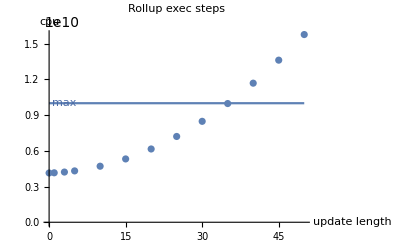

```mathematica
ListPlot[cpuData,PlotRange->All,
PlotLabel->"Rollup exec steps",AxesLabel->{"update length","cpu"}];
Plot[maxExSteps,{x,0,50}];
Graphics[Text[Style["max",RGBColor[0.297856, 0.423621, 0.656168]],{3,maxExSteps},{0,-1}]];
cpuPlot=Show[%%%,%%,%]
```

#### Reaching maximum budget

```mathematica
FindRoot[Interpolation[cpuData][ul]==maxExSteps,{ul,40}]
```

{ul→35.0865}

∴ CPU budget is exceded when update length is ≥ 36 .

### Memory

```mathematica
memData={#⟦1⟧,#⟦3⟧}&/@data
```

{{0,2131374},{1,2152781},{3,2277851},{5,2465929},{10,3199284},{15,4331439},{20,5902394},{25,7852149},{30,10220704},{35,13008059},{40,16194214},{45,19799169},{50,23802924}}

#### Data plot (memory)

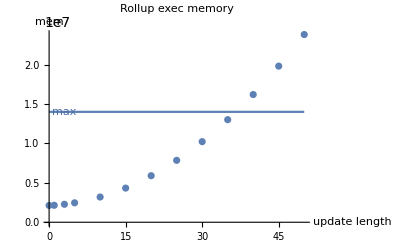

```mathematica
ListPlot[memData,PlotRange->All,
PlotLabel->"Rollup exec memory",AxesLabel->{"update length","mem"}];
Plot[maxExMem,{x,0,50}];
Graphics[Text[Style["max",RGBColor[0.297856, 0.423621, 0.656168]],{3,maxExMem},{0,-1}]];
memPlot=Show[%%%,%%,%]
```

#### Reaching maximum budget

```mathematica
FindRoot[Interpolation[memData][ul]==maxExMem,{ul,40}]
```

{ul→36.6269}

∴ Memory budget is exceded when update length is ≥ 37 .

## Conclusion

To be within exec units budget, update length must be 35 or less.

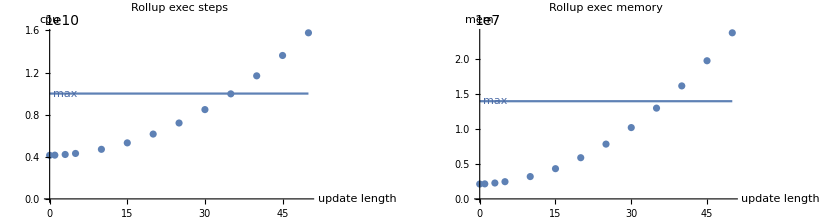

```mathematica
GraphicsRow[{cpuPlot,memPlot}]
```